# GPU execution and CPU comparison

## 缪雨轩 / Miao Yuxuan · 淮南师范学院 / Huainan Normal University

## Model, inputs and scope

Same-input double-precision numerical comparison

SI; exp(+j omega t); RMS; sigma=58 MS/m; mu_r=1; 20 C

Run a small GPU/CPU comparison; retain toolchain and numerical error.

## Derivation and interpretation

Execute the same small double-precision operations on CPU and GPU: matrix multiplication, a complex linear system with known solution and true residual, FFT and inverse roundtrip.

The comparison verifies arithmetic and runtime equivalence for the stated inputs. It does not establish a new physical solution, large-scale convergence or a performance advantage for a different workload.

```mathematica
projectRoot=NestWhile[DirectoryName,NotebookDirectory[],!FileExistsQ[FileNameJoin[{#1,"pyproject.toml"}]]&&DirectoryName[#1]=!=#1&];Get[FileNameJoin[{projectRoot,"shared","wolfram","ResearchNotebook.wl"}]];
```

## Editable parameters

```mathematica
parameters=<|"matrix_size"->128,"fft_size"->4096|>;parameters
```

<|matrix_size -> 128, fft_size -> 4096|>

## Independent execution and results

```mathematica
research=LitzNotebook`RunResearch[projectRoot,"gpu",parameters];LitzNotebook`ResearchSummary[research]
```

<|run_id -> notebook_gpu_20261014010607_2cde71e6, source_model -> gpu, 
 
>   execution_status -> completed, 
 
>   physical_acceptance_status -> passed_test_scope_only|>

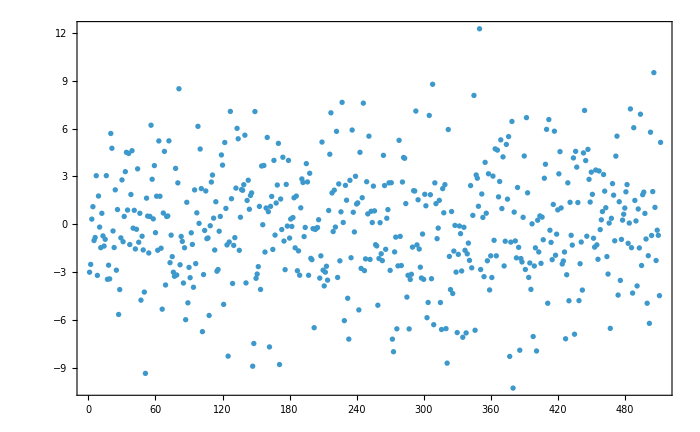

```mathematica
LitzNotebook`DisplayResearch[research]
```

## Acceptance and continuation

Inspect checks, execution_status and physical_acceptance_status. Continue full convergence and structural studies through the route README.

Sources: CUDA; references/library.bib and references/sources.json

## Historical evidence

data/evidence/v1.0.0-rc.1/; litz-research data fetch gpu